# Método de Euler mejorado

En la clase anterior habíamos visto la ecuación diferenciañ y’(t) = 2 x y(t), y(1) = 1

## Solución por el método de Euler

```mathematica
f[x_,y_]:=2 x y;
```

```mathematica
y[x_]:=Exp[x^2-1];
```

```mathematica
xn = 1;
yn = 1;
h = 0.1;
results = {{xn,yn}};

Do[
xnp = xn + h;
ynp= yn + h f[xn,yn];
xn = xnp;
yn = ynp;
AppendTo[results,{xn,yn}];
,10
];
eulerSolution = results;
```

```mathematica
numericSolution = results;
analyticSolution = Table[{x,y[x]},{x,1,2,h}];
```

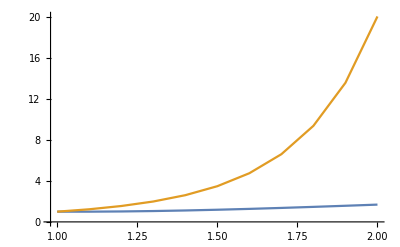

```mathematica
ListLinePlot[{numericSolution,analyticSolution}]
```

## Método de Euler corregido

```mathematica
xn = 1;
yn = 1;
h = 0.1;
results = {{xn,yn}};

Do[
xnp = xn + h;
yAnp= yn + h f[xn,yn];
ynp = yn+ h (f[xn,yn]+f[xn,yAnp])/2;
xn = xnp;
yn = ynp;
AppendTo[results,{xn,yn}];
,10
];
eulerImprovedSolution = results;
```

```mathematica
numericSolution = results;
analyticSolution = Table[{x,y[x]},{x,1,2,h}];
```

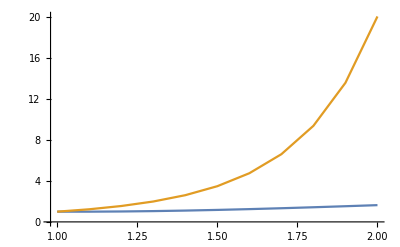

```mathematica
ListLinePlot[{numericSolution,analyticSolution}]
```

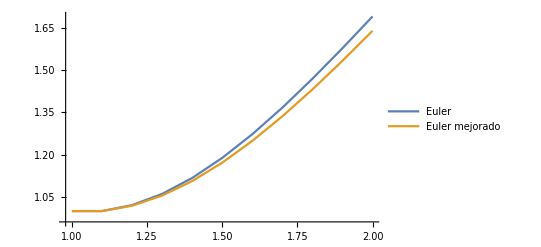

```mathematica
ListLinePlot[{eulerSolution,eulerImprovedSolution},PlotLegends->{"Euler","Euler mejorado"}]
```